#### Heine-Borel Example

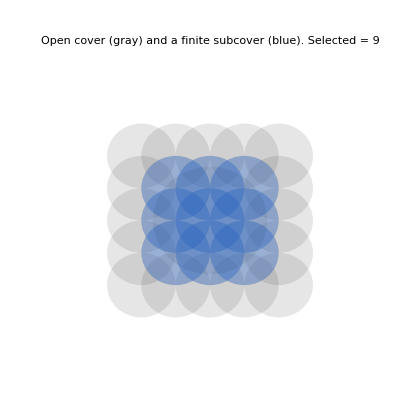
-Graphics--Graphics-

```mathematica
(*---Parameters---*)r=0.60;                               (*radius of the open disks*)
spacing=0.60;                         (*grid spacing for disk centers*)

(*Compact set:closed unit disk sampled on a fine grid*)
regionPts=Select[Flatten[Table[{x,y},{x,-1,1,0.04},{y,-1,1,0.04}],1],Norm[#]<=1&];

(*Open cover:disks centered on a grid*)
centers=Flatten[Table[{i,j},{i,-1.2,1.2,spacing},{j,-1.2,1.2,spacing}],1];

(*Geometric predicates*)
coversQ[c_,p_]:=Norm[p-c]<r;

score[c_,pts_]:=Count[pts,_?(coversQ[c,#]&)];

(*Greedy finite subcover on the sample points*)
remaining=regionPts;
pool=centers;
selected={};

While[remaining=!={}&&pool=!={},best=First@MaximalBy[pool,score[#,remaining]&];
If[score[best,remaining]==0,Print["Increase r or grid density."];Break[];];
AppendTo[selected,best];
remaining=Select[remaining,Not@coversQ[best,#]&];
pool=DeleteCases[pool,best];];

(*---Plots with explicit colors---*)
g0=Graphics[{Directive[Opacity[.12],GrayLevel[0.2]],Disk[#,r]&/@centers,(*entire open cover:gray*)Directive[Opacity[.35],RGBColor[0.2,0.45,0.85]],Disk[#,r]&/@selected,(*finite subcover:blue*)Directive[Opacity[.06],Black],Disk[{0,0},1]                          (*compact set*)},PlotRange->{{-3,3},{-3,3}},ImageSize->420,PlotLabel->Row[{"Open cover (gray) and a finite subcover (blue).  Selected = ",Length[selected]}]];

(*Turn circles into ellipses with a 1+1 Lorentz boost block*)
ϕ=0.9;γ=Cosh[ϕ];sh=Sinh[ϕ];
Λtx={{γ,-sh},{-sh,γ}};

g1=Graphics[GeometricTransformation[{Directive[Opacity[.12],GrayLevel[0.2]],Disk[#,r]&/@centers,Directive[Opacity[.35],RGBColor[0.2,0.45,0.85]],Disk[#,r]&/@selected,Directive[Opacity[.06],Black],Disk[{0,0},1]},Λtx],PlotRange->{{-3,3},{-3,3}},ImageSize->420,PlotLabel->"Images under a Lorentz boost (finite subcover persists)"];

Row[{g0,Spacer[20],g1}]
```

#### Heine-Borel CounterExample

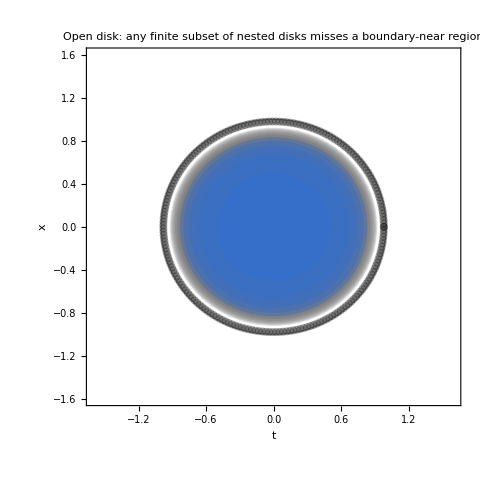
-Graphics--Graphics-

```mathematica
(*----------Parameters& helpers----------*)ClearAll[lt,Λtx]
lt[ϕ_]:=With[{γ=Cosh[ϕ],sh=Sinh[ϕ]},{{γ,-sh},{-sh,γ}}];
Λtx=lt[0.9];                              (*1+1 Lorentz boost block*)

(*----------Open disk cover:nested disks----------*)
Ntotal=12;                                (*how many disks from the infinite cover we draw*)
Nselect=5;                                 (*finite subfamily we highlight*)
radii=Table[1-1/n,{n,2,1+Ntotal}];   (*1/2,2/3,..., ↗1*)
rSel=Take[radii,Nselect];

(*Points near the boundary to show finite subfamilies miss them*)
thetaVals=Subdivide[0,2 Pi,199];
ring=0.98*Transpose[{Cos[thetaVals],Sin[thetaVals]}];  (* <--fixed line*)

(*----------Original-space plot----------*)
gA1=Graphics[{Directive[Opacity[.12],GrayLevel[.2]],Disk[{0,0},#]&/@radii,Directive[Opacity[.35],RGBColor[.2,.45,.85]],Disk[{0,0},#]&/@rSel,Thick,Black,Circle[{0,0},1],Black,PointSize[.012],Point[ring]},PlotRange->{{-1.6,1.6},{-1.6,1.6}},ImageSize->480,Frame->True,FrameLabel->{"t","x"},PlotLabel->"Open disk: any finite subset of nested disks misses a boundary-near region"];

(*----------Boosted plot (disks->ellipses)----------*)
gA2=Graphics[{Directive[Opacity[.12],GrayLevel[.2]],GeometricTransformation[Disk[{0,0},#],Λtx]&/@radii,Directive[Opacity[.35],RGBColor[.2,.45,.85]],GeometricTransformation[Disk[{0,0},#],Λtx]&/@rSel,Thick,Black,GeometricTransformation[Circle[{0,0},1],Λtx],Black,PointSize[.012],GeometricTransformation[Point[ring],Λtx]},PlotRange->{{-3,3},{-3,3}},ImageSize->480,Frame->True,FrameLabel->{"t'","x'"},PlotLabel->"Boosted open disk: finite subset still misses a boundary-near region"];

Row[{gA1,Spacer[18],gA2}]
```

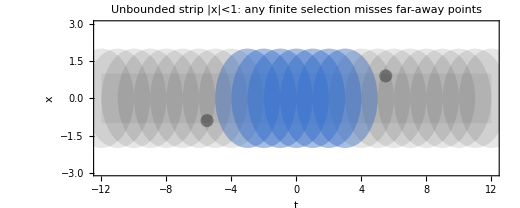
-Graphics--Graphics-

```mathematica
(*----------Parameters& helpers----------*)ClearAll[lt,Λtx]
lt[ϕ_]:=With[{γ=Cosh[ϕ],sh=Sinh[ϕ]},{{γ,-sh},{-sh,γ}}];
Λtx=lt[0.9];

L=12.;     (*plotting half-width along t*)
R=2.;      (*radius of cover disks*)
Nballs=12;   (*draw n=-N..N*)
Mfinite=3;    (*highlight finite subfamily n=-M..M*)

(*Strip polygon in viewing window*)
tVals=Subdivide[-L,L,400];
upper=Transpose[{tVals,ConstantArray[1.,Length@tVals]}];
lower=Transpose[{tVals,ConstantArray[-1.,Length@tVals]}];
stripPoly=Polygon@Join[upper,Reverse@lower];

(*Example uncovered points (far in±t) that any finite subfamily misses*)
uncovered={{Mfinite+2.5,0.9},{-(Mfinite+2.5),-0.9}};

(*----------Original-space plot----------*)
gB1=Graphics[{Directive[Opacity[.06]],stripPoly,Directive[Opacity[.12],GrayLevel[.2]],Table[Disk[{n,0},R],{n,-Nballs,Nballs}],Directive[Opacity[.35],RGBColor[.2,.45,.85]],Table[Disk[{n,0},R],{n,-Mfinite,Mfinite}],Black,PointSize[.018],Point[uncovered]},PlotRange->{{-L,L},{-3,3}},ImageSize->520,Frame->True,FrameLabel->{"t","x"},PlotLabel->"Unbounded strip |x|<1: any finite selection misses far-away points"];

(*----------Boosted plot----------*)
gB2=Graphics[{Directive[Opacity[.06]],GeometricTransformation[stripPoly,Λtx],Directive[Opacity[.12],GrayLevel[.2]],GeometricTransformation[#,Λtx]&/@Table[Disk[{n,0},R],{n,-Nballs,Nballs}],Directive[Opacity[.35],RGBColor[.2,.45,.85]],GeometricTransformation[#,Λtx]&/@Table[Disk[{n,0},R],{n,-Mfinite,Mfinite}],Black,PointSize[.018],GeometricTransformation[Point[uncovered],Λtx]},PlotRange->{{-3,3},{-3,3}},ImageSize->520,Frame->True,FrameLabel->{"t'","x'"},PlotLabel->"Boosted strip: finite selection still misses far-away points"];

Row[{gB1,Spacer[18],gB2}]
```